```mathematica
ClearAll["Global`*"]

wd=SetDirectory@NotebookDirectory[];

stylesVH=Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{9.5,5.5}]];

stylesVH2=Directive[RGBColor[0,0.7,0],AbsoluteThickness[2],AbsoluteDashing[{5,4}]];

stylesblack=Directive[RGBColor[0,0,0],AbsoluteThickness[1.2]];

stylesVAH=Directive[RGBColor[1,0,0],AbsoluteThickness[2]];

stylesdB=Directive[RGBColor[0.6,0,0.6],AbsoluteThickness[2],AbsoluteDashing[{3.2,5}]];

min = {0.0085,0};
maj={0.0145,0};
timeticks = {{0.3,"",min},{0.4,"",min},{0.5,"0.5",maj},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1.0,1,maj},{2,"",min},{3,"",min},{4,"",min},{5,5,maj},{6,"",min},{7,"",min},{8,"",min},{9,"",min},{10,10,maj},{20,"",min},{30,"",min},{40,"",min},{50,50,maj},{60,"",min},{70,"",min},{80,"",min},{90,"",min},{100,100,maj}};

notimeticks = {{0.3,"",min},{0.4,"",min},{0.5,"",maj},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1.0,"",maj},{2,"",min},{3,"",min},{4,"",min},{5,"",maj},{6,"",min},{7,"",min},{8,"",min},{9,"",min},{10,"",maj},{20,"",min},{30,"",min},{40,"",min},{50,"",maj},{60,"",min},{70,"",min},{80,"",min},{90,"",min},{100,"",maj}};


loglogticks = {{0.0001,"",min},{0.0002,"",min},{0.0003,"",min},{0.0004,"",min},{0.0005,"",min},{0.0006,"",min},{0.0007,"",min},{0.0008,"",min},{0.0009,"",min},{0.001,"10^-3",maj},{0.002,"",min},{0.003,"",min},{0.004,"",min},{0.005,"",min},{0.006,"",min},{0.007,"",min},{0.008,"",min},{0.009,"",min},{0.01,"0.01",maj},
{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},{0.1,0.1,maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1,1,maj}};

nologlogticks = {{0.0001,"",min},{0.0002,"",min},{0.0003,"",min},{0.0004,"",min},{0.0005,"",min},{0.0006,"",min},{0.0007,"",min},{0.0008,"",min},{0.0009,"",min},{0.001,"",maj},{0.002,"",min},{0.003,"",min},{0.004,"",min},{0.005,"",min},{0.006,"",min},{0.007,"",min},{0.008,"",min},{0.009,"",min},{0.01,"",maj},
{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},{0.1,"",maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1,"",maj}};


(*//////////////////////////////////////////////////////////////*)

EnergyDensityDataRawVH=Import[wd<>"/eplot_vh.dat"];
piDataRawVH=Import[wd<>"/piplot_vh.dat"];
PiDataRawVH=Import[wd<>"/bulkplot_vh.dat"];
plptDataRawVH=Import[wd<>"/plptplot_vh.dat"];
BDataRawVH=Import[wd<>"/Bplot_vh.dat"];
dB2ndDataRawVH=Import[wd<>"/dB2ndplot_vh.dat"];

EnergyDensityDataVH= Take[EnergyDensityDataRawVH,{2,Length[EnergyDensityDataRawVH]}];
piDataVH= Take[piDataRawVH,{2,Length[piDataRawVH]}];
PiDataVH= Take[PiDataRawVH,{2,Length[PiDataRawVH]}];
plptDataVH= Take[plptDataRawVH,{2,Length[plptDataRawVH]}];
BDataVH= Take[BDataRawVH,{2,Length[BDataRawVH]}];
dB2ndDataVH= Take[dB2ndDataRawVH,{2,Length[dB2ndDataRawVH]}];

energydensityVH = Interpolation[EnergyDensityDataVH[[All,{1,2}]]];
piVH = Interpolation[piDataVH[[All,{1,2}]]];
bulkVH = Interpolation[PiDataVH[[All,{1,2}]]];
plptVH = Interpolation[plptDataVH[[All,{1,2}]]];
BVH = Interpolation[BDataVH[[All,{1,2}]]];
dB2ndVH = Interpolation[dB2ndDataVH[[All,{1,2}]]];



(*//////////////////////////////////////////////////////////////*)


EnergyDensityDataRawVH2=Import[wd<>"/eplot_vh2.dat"];
piDataRawVH2=Import[wd<>"/piplot_vh2.dat"];
PiDataRawVH2=Import[wd<>"/bulkplot_vh2.dat"];
plptDataRawVH2=Import[wd<>"/plptplot_vh2.dat"];
BDataRawVH2=Import[wd<>"/Bplot_vh2.dat"];
dB2ndDataRawVH2=Import[wd<>"/dB2ndplot_vh2.dat"];


EnergyDensityDataVH2= Take[EnergyDensityDataRawVH2,{2,Length[EnergyDensityDataRawVH2]}];
piDataVH2= Take[piDataRawVH2,{2,Length[piDataRawVH2]}];
PiDataVH2= Take[PiDataRawVH2,{2,Length[PiDataRawVH2]}];
plptDataVH2= Take[plptDataRawVH2,{2,Length[plptDataRawVH2]}];
BDataVH2= Take[BDataRawVH2,{2,Length[BDataRawVH2]}];
dB2ndDataVH2= Take[dB2ndDataRawVH2,{2,Length[dB2ndDataRawVH2]}];

energydensityVH2 = Interpolation[EnergyDensityDataVH2[[All,{1,2}]]];
piVH2 = Interpolation[piDataVH2[[All,{1,2}]]];
bulkVH2 =Interpolation[PiDataVH2[[All,{1,2}]]];
plptVH2 = Interpolation[plptDataVH2[[All,{1,2}]]];
BVH2 = Interpolation[BDataVH2[[All,{1,2}]]];
dB2ndVH2 = Interpolation[dB2ndDataVH2[[All,{1,2}]]];


(*//////////////////////////////////////////////////////////////*)
(*NAVIER STOKES*)

PiNSDataRawVH=Import[wd<>"/bulkNSplot_vh.dat"];
PiNSDataVH= Take[PiNSDataRawVH,{2,Length[PiNSDataRawVH]}];
bulkNSVH = Interpolation[PiNSDataVH[[All,{1,2}]]];

piNSDataRawVH=Import[wd<>"/piNSplot_vh.dat"];
piNSDataVH= Take[piNSDataRawVH,{2,Length[piNSDataRawVH]}];
piNSVH = Interpolation[piNSDataVH[[All,{1,2}]]];




PiNSDataRawVH2=Import[wd<>"/bulkNSplot_vh2.dat"];
PiNSDataVH2= Take[PiNSDataRawVH2,{2,Length[PiNSDataRawVH2]}];
bulkNSVH2 = Interpolation[PiNSDataVH2[[All,{1,2}]]];

piNSDataRawVH2=Import[wd<>"/piNSplot_vh2.dat"];
piNSDataVH2= Take[piNSDataRawVH2,{2,Length[piNSDataRawVH2]}];
piNSVH2 = Interpolation[piNSDataVH2[[All,{1,2}]]];




PiNSDataRawVAH=Import[wd<>"/bulkNSplot_vah.dat"];
PiNSDataVAH= Take[PiNSDataRawVAH,{2,Length[PiNSDataRawVAH]}];
bulkNSVAH = Interpolation[PiNSDataVAH[[All,{1,2}]]];

piNSDataRawVAH=Import[wd<>"/piNSplot_vah.dat"];
piNSDataVAH= Take[piNSDataRawVAH,{2,Length[piNSDataRawVAH]}];
piNSVAH = Interpolation[piNSDataVAH[[All,{1,2}]]];
(*//////////////////////////////////////////////////////////////*)


EnergyDensityDataRawVAH=Import[wd<>"/eplot_vah.dat"];
piDataRawVAH=Import[wd<>"/piplot_vah.dat"];
PiDataRawVAH=Import[wd<>"/bulkplot_vah.dat"];
plptDataRawVAH=Import[wd<>"/plptplot_vah.dat"];
BDataRawVAH=Import[wd<>"/Bplot_vah.dat"];
BeqDataRawVAH=Import[wd<>"/Beqplot_vah.dat"];
dBasyDataRawVAH=Import[wd<>"/dBasyplot_vah.dat"];

EnergyDensityDataVAH= Take[EnergyDensityDataRawVAH,{2,Length[EnergyDensityDataRawVAH]}];
piDataVAH= Take[piDataRawVAH,{2,Length[piDataRawVAH]}];
PiDataVAH= Take[PiDataRawVAH,{2,Length[PiDataRawVAH]}];
plptDataVAH= Take[plptDataRawVAH,{2,Length[plptDataRawVAH]}];
BDataVAH= Take[BDataRawVAH,{2,Length[BDataRawVAH]}];
BeqDataVAH= Take[BeqDataRawVAH,{2,Length[BeqDataRawVAH]}];
dBasyDataVAH= Take[dBasyDataRawVAH,{2,Length[dBasyDataRawVAH]}];


energydensityVAH = Interpolation[EnergyDensityDataVAH[[All,{1,2}]]];
piVAH = Interpolation[piDataVAH[[All,{1,2}]]];
bulkVAH = Interpolation[PiDataVAH[[All,{1,2}]]];
plptVAH = Interpolation[plptDataVAH[[All,{1,2}]]];
BVAH = Interpolation[BDataVAH[[All,{1,2}]]];
BeqVAH = Interpolation[BeqDataVAH[[All,{1,2}]]];
dBasyVAH = Interpolation[dBasyDataVAH[[All,{1,2}]]];


t0 = EnergyDensityDataVAH[[1,1]];
tf = EnergyDensityDataVAH[[Length[EnergyDensityDataVAH],1]];

legend1=Panel[Grid[{{Graphics[{stylesVH,Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["vHydro",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{stylesVH2,Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["vHydro 2",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{stylesVAH,Line[{{0,0},{1,0}}]},ImageSize->26
,AspectRatio->0.2],Style["vaHydro",FontSize->14,FontFamily->"Calibri"]}}],Background->White,FrameMargins->0];

legend2=Panel[Grid[{{Graphics[{stylesVH,Line[{{0,0},{1,0}}]},ImageSize->28,AspectRatio->0.2],Style["vHydro",FontSize->16,FontFamily->"Calibri"]},
{Graphics[{stylesVAH,Line[{{0,0},{1,0}}]},ImageSize->28
,AspectRatio->0.2],Style["vaHydro",FontSize->16,FontFamily->"Calibri"]}}],Background->White,FrameMargins->0];

legend3=Panel[Grid[{{Graphics[{stylesdB,Line[{{0,0},{1,0}}]},ImageSize->25,AspectRatio->0.2],Style["δB^(asy)",FontSize->16,FontFamily->"Calibri"]}}],Background->White,FrameMargins->0];


legendtau=Panel[Style["(τ_0/τ)^(4/3)",FontSize->13,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendenergy=Panel[Style["ℰ/ℰ_0",FontSize->20,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendpi=Panel[Style["π",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendbulk=Panel[Style["Π",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendplpt=Panel[Style["P_L/(P_⊥)",FontSize->20,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendB=Panel[Style["B",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legenddB=Panel[Style["δB",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
```

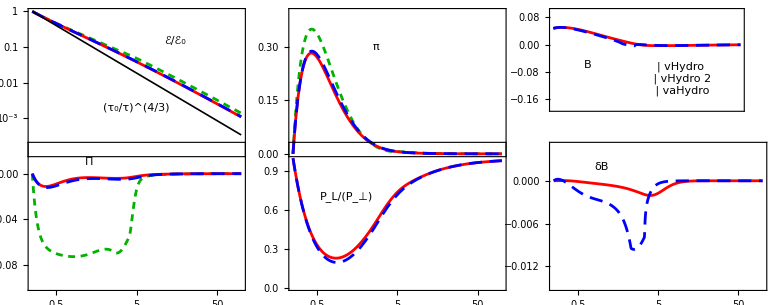
-Graphics-τ (fm/c)

```mathematica
a=40;
b=20;


energyplot=LogLogPlot[{energydensityVH2[t],energydensityVAH[t],energydensityVH[t],(t0/t)^(4/3)},{t,t0,tf},PlotRange->{0.0001,1},PlotStyle->{stylesVH2,stylesVAH,stylesVH,stylesblack},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{loglogticks,nologlogticks},{notimeticks,timeticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendenergy,{2.7,-1.9}],Inset[legendtau,{1.6,-6.2}](*,Inset[Style["(a)",FontSize->14,FontFamily->"Calibri"],{3.9,-8.1}]*)},ImagePadding->{{a,b},{Automatic,Automatic}}];

bulkplot=LogLinearPlot[{0.197327*bulkVH2[t],0.197327*bulkVAH[t],0.197327*bulkVH[t]},{t,t0,tf},PlotRange->{-0.1,0.025},PlotStyle->{stylesVH2,stylesVAH,stylesVH},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{timeticks,notimeticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendbulk,{0.25,0.01}](*,Inset[Style["(d)",FontSize->14,FontFamily->"Calibri"],{3.9,-0.052}]*)},ImagePadding->{{a,b},{Automatic,Automatic}}];

piplot =LogLinearPlot[{0.197327*piVH2[t],0.197327*piVAH[t],0.197327*piVH[t]},{t,t0,tf},PlotRange->{0,0.4},PlotStyle->{stylesVH2,stylesVAH,stylesVH},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{notimeticks,timeticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendpi,{1.,0.3}](*,Inset[Style["(b)",FontSize->14,FontFamily->"Calibri"],{3.9,0.9}]*)},ImagePadding->{{a,b},{Automatic,Automatic}}];

plptplot =LogLinearPlot[{plptVAH[t],plptVH[t]},{t,t0,tf},PlotRange->{0,1.1},PlotStyle->{stylesVAH,stylesVH},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{timeticks,notimeticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendplpt,{0.14,0.7}](*,Inset[Style["(e)",FontSize->14,FontFamily->"Calibri"],{3.9,0.3}]*)},ImagePadding->{{a,b},{Automatic,Automatic}}];

Bplot = LogLinearPlot[{0.197327*BVAH[t],0.197327* BVH[t]},{t,t0,tf},PlotRange->{-0.19,0.1},PlotStyle->{stylesVAH,stylesVH},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{notimeticks,timeticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legend1,{2.7,-0.1}],Inset[legendB,{-0.3,-0.06}],Inset[Style["(c)",FontSize->14,FontFamily->"Calibri"],{3.9,-2.22}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

dBplot=LogLinearPlot[{0.197327*(BVAH[t]-BeqVAH[t]),0.197327*dB2ndVH[t]},{t,t0,tf},PlotRange->{-0.015,0.005},PlotStyle->{stylesVAH,stylesVH},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{timeticks,notimeticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{(*Inset[legend3,{0.7,-0.008}],*)Inset[legenddB,{-0.,0.002}](*,Inset[Style["(f)",FontSize->14,FontFamily->"Calibri"],{3.9,-0.0083}]*)},ImagePadding->{{a,b},{Automatic,Automatic}}]; 


a1=Panel[GraphicsGrid[{{energyplot,piplot,Bplot},{bulkplot,plptplot,dBplot}},Spacings->{5,-41}],Style["τ (fm/c)",FontFamily->"Calibri",FontSize->14],{{Bottom,Center}},Appearance->"Frameless",Background->White,ImageSize->{742,300},FrameMargins->0]

Export["compare_hydro.pdf",a1];
```

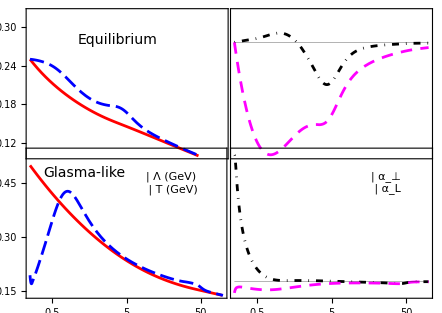
-Graphics-τ (fm/c)

```mathematica
(*Equilibrium*)

TDataRaw=Import[wd<>"/Tplot_vah.dat"];
lambdaDataRaw=Import[wd<>"/lambdaplot_vah.dat"];
axDataRaw=Import[wd<>"/axplot_vah.dat"];
azDataRaw=Import[wd<>"/azplot_vah.dat"];

TData= Take[TDataRaw,{2,Length[TDataRaw]}];
lambdaData= Take[lambdaDataRaw,{2,Length[lambdaDataRaw]}];
axData= Take[axDataRaw,{2,Length[axDataRaw]}];
azData= Take[azDataRaw,{2,Length[azDataRaw]}];

T = Interpolation[TData[[All,{1,2}]]];
lambda = Interpolation[lambdaData[[All,{1,2}]]];
ax = Interpolation[axData[[All,{1,2}]]];
az = Interpolation[azData[[All,{1,2}]]];


(*Glasma*)

TDataRaw2=Import[wd<>"/Tplot_vah2.dat"];
lambdaDataRaw2=Import[wd<>"/lambdaplot_vah2.dat"];
axDataRaw2=Import[wd<>"/axplot_vah2.dat"];
azDataRaw2=Import[wd<>"/azplot_vah2.dat"];

TData2= Take[TDataRaw2,{2,Length[TDataRaw2]}];
lambdaData2= Take[lambdaDataRaw2,{2,Length[lambdaDataRaw2]}];
axData2= Take[axDataRaw2,{2,Length[axDataRaw2]}];
azData2= Take[azDataRaw2,{2,Length[azDataRaw2]}];

T2 = Interpolation[TData2[[All,{1,2}]]];
lambda2 = Interpolation[lambdaData2[[All,{1,2}]]];
ax2 = Interpolation[axData2[[All,{1,2}]]];
az2 = Interpolation[azData2[[All,{1,2}]]];

stylesVAH={Directive[RGBColor[1,0,0],AbsoluteThickness[2]],Directive[RGBColor[1,0,0],AbsoluteThickness[2]],
Directive[RGBColor[1,0,0],AbsoluteThickness[2]],Directive[RGBColor[1,0,0],AbsoluteThickness[2]]};

legendtemp=Panel[Grid[{{Graphics[{Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{10,4}]],Line[{{0,0},{1,0}}]},ImageSize->26.0,AspectRatio->0.2],Style["Λ (GeV)",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{Directive[RGBColor[1,0,0],AbsoluteThickness[2]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["T (GeV)",FontSize->14,FontFamily->"Calibri"]}}],Background->White,FrameMargins->0];

legendalpha=Panel[Grid[{{Graphics[{Directive[RGBColor[0,0,0],AbsoluteThickness[2],DotDashed],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["α_⊥",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{Directive[RGBColor[1,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["α_L",FontSize->14,FontFamily->"Calibri"]}}],Background->White,FrameMargins->0];

noalphaticks1 = {{0.52,"",min},{0.54,"",min},{0.56,"",min},{0.58,"",min},{0.6,"",maj},{0.62,"",min},{0.64,"",min},{0.66,"",min},{0.68,"",min},{0.7,"",maj},{0.72,"",min},{0.74,"",min},{0.76,"",min},{0.78,"",min},{0.8,"",maj},{0.82,"",min},{0.84,"",min},{0.86,"",min},{0.88,"",min},{0.9,"",maj},{0.92,"",min},{0.94,"",min},{0.96,"",min},{0.98,"",min},{1.0,"",maj},{1.02,"",min},{1.04,"",min},{1.06,"",min},{1.08,"",min},{1.1,"",maj},{1.12,"",min}};

noalphaticks2 = {{0.5,"",min},{1.0,"",min},{1.5,"",min},{2.0,"",maj},
{2.5,"",min},{3.0,"",min},{3.5,"",min},{4.0,"",maj},
{4.5,"",min},{5.0,"",min},{5.5,"",min},{6.0,"",maj},
{6.5,"",min},{7.0,"",min},{7.5,"",min},{8.0,"",maj},
{8.5,"",min},{9.0,"",min},{9.5,"",min},{10.0,"",maj}
};




temp1=LogLinearPlot[{0.197327*T[t],0.197327*lambda[t]},{t,t0,tf},PlotRange->{0.1,0.6*0.54},PlotStyle->{Directive[RGBColor[1,0,0],AbsoluteThickness[2]],Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{10.2,4.3}]]},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{notimeticks,timeticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[Style["Equilibrium",FontSize->14,FontFamily->"Calibri"],{1.3,0.28}](*,Inset[Style["(a)",FontSize->14,FontFamily->"Calibri"],{3.9,0.22}]*)},ImagePadding->{{25,20},{Automatic,Automatic}}];

alpha1=LogLinearPlot[{ax[t],az[t],1},{t,t0,tf},PlotRange->{0.52,1.13},PlotStyle->{Directive[RGBColor[0,0,0],AbsoluteThickness[2],DotDashed],Directive[RGBColor[1,0,1],AbsoluteThickness[2],AbsoluteDashing[{8.25,6}]],Directive[Black,AbsoluteThickness[0.21]]},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{noalphaticks1,All},{notimeticks,timeticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,(*Epilog->{Inset[Style["(b)",FontSize->14,FontFamily->"Calibri"],{3.9,0.645}]},*)ImagePadding->{{25,20},{Automatic,Automatic}}];

temp2=LogLinearPlot[{0.197327*T2[t],0.197327*lambda2[t]},{t,t0,tf},PlotRange->{0.1367,0.54},PlotStyle->{Directive[RGBColor[1,0,0],AbsoluteThickness[2]],Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{10.2,4.1}]]},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{timeticks,notimeticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[Style["Glasma-like",FontSize->14,FontFamily->"Calibri"],{0.3,0.48}],Inset[legendtemp,{3,0.45}](*,Inset[Style["(c)",FontSize->14,FontFamily->"Calibri"],{3.9,0.22}]*)},ImagePadding->{{25,20},{Automatic,Automatic}}];

alpha2=LogLinearPlot[{ax2[t],az2[t],1},{t,t0,tf},PlotRange->{0,10.5},PlotStyle->{Directive[Black,AbsoluteThickness[2],DotDashed],Directive[RGBColor[1,0,1],AbsoluteThickness[2],AbsoluteDashing[{8.25,6}]],Directive[Black,AbsoluteThickness[.21]]},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{noalphaticks2,All},{timeticks,notimeticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendalpha,{3.3,8.2}](*,Inset[Style["(d)",FontSize->14,FontFamily->"Calibri"],{3.9,2.2}]*)},ImagePadding->{{25,20},{Automatic,Automatic}}];

anisoplot=Panel[GraphicsGrid[{{temp1,alpha1},{temp2,alpha2}},Spacings->{-35,-36.8}],Style["τ (fm/c)",FontFamily->"Calibri",FontSize->14],{{Bottom,Center}},Appearance->"Frameless",Background->White,ImageSize->{450,310},FrameMargins->0]

Export["aniso.pdf",anisoplot];
```

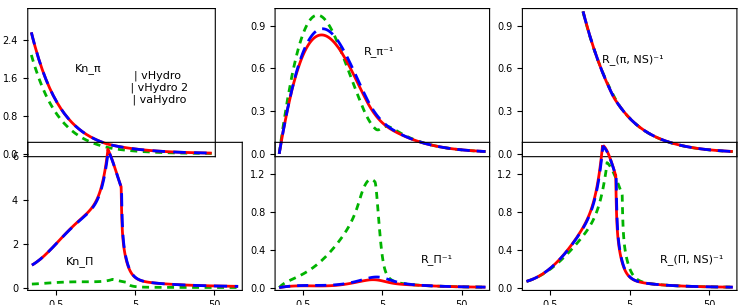
-Graphics-τ (fm/c)

```mathematica
RpiInverseDataRawVH=Import[wd<>"/RpiInvplot_vh.dat"];
RbulkInverseDataRawVH=Import[wd<>"/RbulkInvplot_vh.dat"];

RpiInverseDataVH= Take[RpiInverseDataRawVH,{2,Length[RpiInverseDataRawVH]}];
RbulkInverseDataVH= Take[RbulkInverseDataRawVH,{2,Length[RbulkInverseDataRawVH]}];

RpiInverseVH = Interpolation[RpiInverseDataVH[[All,{1,2}]]];
RbulkInverseVH = Interpolation[RbulkInverseDataVH[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

RpiInverseDataRawVH2=Import[wd<>"/RpiInvplot_vh2.dat"];
RbulkInverseDataRawVH2=Import[wd<>"/RbulkInvplot_vh2.dat"];

RpiInverseDataVH2= Take[RpiInverseDataRawVH2,{2,Length[RpiInverseDataRawVH2]}];
RbulkInverseDataVH2= Take[RbulkInverseDataRawVH2,{2,Length[RbulkInverseDataRawVH2]}];

RpiInverseVH2 = Interpolation[RpiInverseDataVH2[[All,{1,2}]]];
RbulkInverseVH2 = Interpolation[RbulkInverseDataVH2[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

RpiInverseDataRawVAH=Import[wd<>"/RpiInvplot_vah.dat"];
RbulkInverseDataRawVAH=Import[wd<>"/RbulkInvplot_vah.dat"];

RpiInverseDataVAH= Take[RpiInverseDataRawVAH,{2,Length[RpiInverseDataRawVAH]}];
RbulkInverseDataVAH= Take[RbulkInverseDataRawVAH,{2,Length[RbulkInverseDataRawVAH]}];

RpiInverseVAH = Interpolation[RpiInverseDataVAH[[All,{1,2}]]];
RbulkInverseVAH = Interpolation[RbulkInverseDataVAH[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

taupiDataRawVH=Import[wd<>"/taupiplot_vh.dat"];
taubulkDataRawVH=Import[wd<>"/taubulkplot_vh.dat"];

taupiDataVH= Take[taupiDataRawVH,{2,Length[taupiDataRawVH]}];
taubulkDataVH= Take[taubulkDataRawVH,{2,Length[taubulkDataRawVH]}];

taupiVH = Interpolation[taupiDataVH[[All,{1,2}]]];
taubulkVH = Interpolation[taubulkDataVH[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

taupiDataRawVH2=Import[wd<>"/taupiplot_vh2.dat"];
taubulkDataRawVH2=Import[wd<>"/taubulkplot_vh2.dat"];

taupiDataVH2= Take[taupiDataRawVH2,{2,Length[taupiDataRawVH2]}];
taubulkDataVH2= Take[taubulkDataRawVH2,{2,Length[taubulkDataRawVH2]}];

taupiVH2 = Interpolation[taupiDataVH2[[All,{1,2}]]];
taubulkVH2 = Interpolation[taubulkDataVH2[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

taupiDataRawVAH=Import[wd<>"/taupiplot_vah.dat"];
taubulkDataRawVAH=Import[wd<>"/taubulkplot_vah.dat"];

taupiDataVAH= Take[taupiDataRawVAH,{2,Length[taupiDataRawVAH]}];
taubulkDataVAH= Take[taubulkDataRawVAH,{2,Length[taubulkDataRawVAH]}];

taupiVAH = Interpolation[taupiDataVAH[[All,{1,2}]]];
taubulkVAH = Interpolation[taubulkDataVAH[[All,{1,2}]]];




legendRbulk=Panel[Style["R_Π^-1",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendRpi=Panel[Style["R_π^-1",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendRbulkNS=Panel[Style["R_(Π, NS)^-1",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendRpiNS=Panel[Style["R_(π, NS)^-1",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendKnbulk=Panel[Style["Kn_Π",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendKnpi=Panel[Style["Kn_π",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];

a=30;
b = 20;


Knpi=LogLinearPlot[{Sqrt[2./3.]*taupiVH2[t]/t,Sqrt[2./3.]*taupiVAH[t]/t,Sqrt[2./3.]*taupiVH[t]/t},{t,t0,tf-0.005},PlotRange->{0,3},PlotStyle->{stylesVH2,stylesVAH,Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{9,6}]]},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{notimeticks,timeticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legend1,{2.8,1.4}],Inset[legendKnpi,{0.5,1.8}](*,Inset[Style["(a)",FontSize->14,FontFamily->"Calibri"],{3.4,0.48}]*)},ImagePadding->{{a,b},{Automatic,Automatic}}];

Knbulk=LogLinearPlot[{taubulkVH2[t]/t,taubulkVAH[t]/t,taubulkVH[t]/t},{t,t0,tf-0.005},PlotRange->{0,6.5},PlotStyle->{stylesVH2,stylesVAH,stylesVH},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{timeticks,notimeticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendKnbulk,{-0.0,1.2}](*,Inset[Style["(d)",FontSize->14,FontFamily->"Calibri"],{3.4,0.13}]*)},ImagePadding->{{a,b},{Automatic,Automatic}}];

Rpi=LogLinearPlot[{RpiInverseVH2[t],RpiInverseVAH[t],RpiInverseVH[t]},{t,t0,tf},PlotRange->{-0.00,1},PlotStyle->{stylesVH2,stylesVAH,Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{9,5}]]},ImageSize->250,Frame->True,Axes->False,RotateLabel->False,FrameTicks->{{All,True},{notimeticks,timeticks}},(*,FrameLabel->{"",Style["R_π^-1",FontSize->16,FontFamily->"Calibri"]},*)BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{(*Inset[Style["(b)",FontSize->14,FontFamily->"Calibri"],{3.4,0.13}],*)Inset[legendRpi,{1.5,0.72}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

Rbulk=LogLinearPlot[{Abs[RbulkInverseVH2[t]],Abs[RbulkInverseVAH[t]],Abs[RbulkInverseVH[t]]},{t,t0,tf},PlotRange->{-0.00,1.5},PlotStyle->{stylesVH2,stylesVAH,Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,5.}]]},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{timeticks,notimeticks}},RotateLabel->False(*FrameLabel->{"","","",Style["R_Π^-1",FontSize->16,FontFamily->"Calibri"]}*),BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendRbulk,{3.2,0.3}](*,Inset[Style["(e)",FontSize->14,FontFamily->"Calibri"],{3.4,0.017}]*)},ImagePadding->{{a,b},{Automatic,Automatic}}];

RpiNS=LogLinearPlot[{piNSVH2[t],piNSVAH[t],piNSVH[t]},{t,t0,tf},PlotRange->{0.00,1},PlotStyle->{stylesVH2,stylesVAH,Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{9,5}]]},ImageSize->250,Frame->True,Axes->False,RotateLabel->False,FrameTicks->{{All,True},{notimeticks,timeticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{(*Inset[Style["(c)",FontSize->14,FontFamily->"Calibri"],{3.4,0.13}],*)Inset[legendRpiNS,{1.7,0.66}]},ImagePadding->{{a,b},{Automatic,Automatic}},GridLines->None];

RbulkNS=LogLinearPlot[{Abs[bulkNSVH2[t]],Abs[bulkNSVAH[t]],Abs[bulkNSVH[t]]},{t,t0,tf},PlotRange->{-0.00,1.5},PlotStyle->{stylesVH2,stylesVAH,Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{9,5.3}]]},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{timeticks,notimeticks}},RotateLabel->False,BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendRbulkNS,{3.4,0.3}](*,Inset[Style["(f)",FontSize->14,FontFamily->"Calibri"],{3.4,0.017}]*)},ImagePadding->{{a,b},{Automatic,Automatic}}];


(*a3=Panel[GraphicsGrid[{{Rpi,Rbulk},{Knpi,Knbulk}},Spacings->{-49,-24.3}],Style["τ (fm/c)",FontFamily->"Calibri",FontSize->14],{{Bottom,Center}},Background->White,ImageSize->{420,325},FrameMargins->0]
*)
a3=Panel[GraphicsGrid[{{Knpi,Rpi,RpiNS},{Knbulk,Rbulk,RbulkNS}},Spacings->{-5,-41.}],Style["τ (fm/c)",FontFamily->"Calibri",FontSize->14],{{Bottom,Center}},Background->White,ImageSize->{743,305},FrameMargins->0]

Export["compare_validity.pdf",a3];
```